-0.316228

-1.

0.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

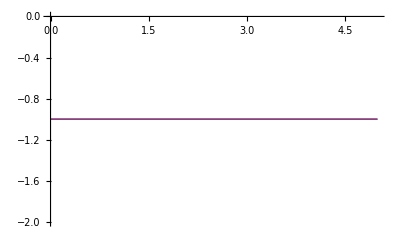

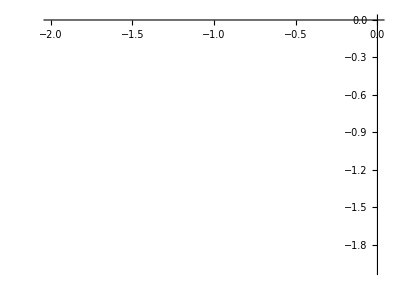

```mathematica
Needs["VariationalMethods`"];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
gamma=1/10;
delta1=1/10;
delta2=1/10;
tmin=0.0001;
tmax=5;
V[x[t_],y[t_]]:=(x[t]^2-1)^2(x[t]^2-delta1)+((y[t]^2-1)^2-(delta2(y[t]-2)(y[t]+1)^2)/4)/(x[t]^2+gamma);
U[x_,y_]:=(x^2-1)^2(x^2-delta1)+((y^2-1)^2-delta2(y-2)(y+1)^2/4)/(x^2+gamma);
ftn=2*Pi*t*(1/2(D[x[t],t]^2+D[y[t],t]^2)+V[x[t],y[t]]); (* Le Lagrangien *)
Veff[x_]:=U[x,-1];
x0=x/.FindRoot[Veff[x]==U[-1,-1],{x,-0.2}]
(*sln=D[x[t],t,t]+D[x[t],t]/t==8(1+x[t])(1-delta1),D[y[t],t,t]+D[y[t],t]/t==2(1+y[t])(3delta2/4-4)/(1+gamma);*)
solution=NDSolve[{D[x[t],t,t]+D[x[t],t]/t==8(1+x[t])(1-delta1),D[y[t],t,t]+D[y[t],t]/t==2(1+y[t])(3delta2/4-4)/(1+gamma),x[tmin]==-1,y[tmin]==-1,x'[tmax]==0,y[tmax]==-1},{x[t],y[t]},{t,tmin,tmax},Method->{"Shooting","StartingInitialConditions"->{x[tmin]==-1,x'[tmin]==0,y[tmin]==-1,y'[tmin]==0}}];
psi[t_]=x[t]/.solution[[1,1]];
phi[t_]=y[t]/.solution[[1,2]];
psi[tmax]
D[psi[t],t]/.t->tmax
action=NIntegrate[2*Pi*t(1/2(D[psi[t],t]^2+D[phi[t],t]^2)+((psi[t]^2-1)^2(psi[t]^2-delta1)+((phi[t]^2-1)^2-delta2(phi[t]-2)(phi[t]+1)^2/4)/(psi[t]^2+gamma))),{t,tmin,tmax}];
lp2=Plot[{psi[t],phi[t]},{t,tmin,tmax},PlotRange->All]
sep=ParametricPlot[{psi[t],phi[t]},{t,tmin,tmax},PlotRange->All]
```